# Hatsuda QNMs Method

Lectures on Resurgence, University of Alabama, 2020

Author: Marco Knipfer
Reproducing the paper: 1906.07232 (author: Hatsuda)

## 0) Some variables and functions

```mathematica
prec= 200;
order = 50;
tempOrder = 2 order + 2;
padeOrder = order/2;
```

## 1) Metric and Differential Equation

```mathematica
r0metric = 1;
d = 4;
l = 0;
s = 0;
n = 0;
```

```mathematica
f[r_] :=1 - (r0metric/r)^(d-3) (*+ r^2/R^2*);
Vgeneral[r_, fgeneral_] := ((d-2)(d-4))/(4 r^2)fgeneral[r] + (d-2)/(2r)(1-s^2)fgeneral'[r] + l(l+d-3)/r^2;
V[r_] :=  f[r]Vgeneral[r, f]//Simplify;
```

```mathematica
V[r] (*Regge-Wheeler potential*)
```

(-1+r)/r^4

The differential equation has the form
(ϵ^2 d^2/(dr_*)^2 + ω^2- V(r(r_*)))ϕ(r_*) = 0

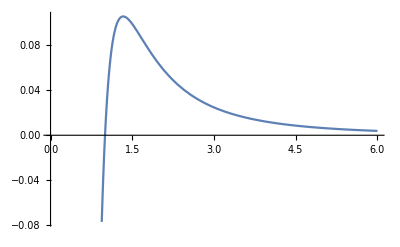

```mathematica
Plot[V[r], {r,0,6}]
```

next we would have to transform ℏ=iϵ, E=-ω^2 to invert the potential, but we do this implicitly later.

## 2) Shift so that minimum of V is at zero, expand around it

```mathematica
r0 = r/.FindRoot[D[V[r],r] == 0, {r, 1.5}, WorkingPrecision->prec];
```

```mathematica
r0//N
```

1.33333

Tortoise coordinate r_*(r)
- r_(*0) = r_*(r0)
- r = r_0+δ
- r_* = r_(*0)+ δ_*(δ)
- δ(δ_*)

This is a trick to calculate the tortoise coordinate  V(r_0+δ(δ_*)).

```mathematica
δsSeries = (Series[1/f[r0+δδ], {δδ, 0, tempOrder}, Assumptions->{δδ∈Reals}]*δδ)/.{δδ->δ};
δsSeries2 =((Normal@ δsSeries)/.{δ^nn_ -> δ^nn / nn})+ O[δ]^(tempOrder+1);
```

```mathematica
δsSeries2//N
```

4. (δ+0.)-4.5 (δ+0.)^2+9. (δ+0.)^3-20.25 (δ+0.)^4+48.6 (δ+0.)^5-121.5 (δ+0.)^6+312.429 (δ+0.)^7-820.125 (δ+0.)^8+2187. (δ+0.)^9-5904.9 (δ+0.)^10+16104.3 (δ+0.)^11-44286.8 (δ+0.)^12+122640. (δ+0.)^13-341641. (δ+0.)^14+956594. (δ+0.)^15-2.69042×10^6 (δ+0.)^16+7.59648×10^6 (δ+0.)^17-2.15234×10^7 (δ+0.)^18+6.11717×10^7 (δ+0.)^19-1.74339×10^8 (δ+0.)^20+4.98112×10^8 (δ+0.)^21-1.42641×10^9 (δ+0.)^22+4.09318×10^9 (δ+0.)^23-1.17679×10^10 (δ+0.)^24+3.38915×10^10 (δ+0.)^25-9.77641×10^10 (δ+0.)^26+2.8243×10^11 (δ+0.)^27-8.17028×10^11 (δ+0.)^28+2.36656×10^12 (δ+0.)^29-6.86304×10^12 (δ+0.)^30+1.99249×10^13 (δ+0.)^31-5.79069×10^13 (δ+0.)^32+1.68456×10^14 (δ+0.)^33-4.90505×10^14 (δ+0.)^34+1.42947×10^15 (δ+0.)^35-4.1693×10^15 (δ+0.)^36+1.21698×10^16 (δ+0.)^37-3.55487×10^16 (δ+0.)^38+1.03912×10^17 (δ+0.)^39-3.03942×10^17 (δ+0.)^40+8.89585×10^17 (δ+0.)^41-2.60521×10^18 (δ+0.)^42+7.63388×10^18 (δ+0.)^43-2.23812×10^19 (δ+0.)^44+6.56514×10^19 (δ+0.)^45-1.92673×10^20 (δ+0.)^46+5.65719×10^20 (δ+0.)^47-1.6618×10^21 (δ+0.)^48+4.88366×10^21 (δ+0.)^49-1.4358×10^22 (δ+0.)^50+4.22293×10^22 (δ+0.)^51-1.24252×10^23 (δ+0.)^52+3.65722×10^23 (δ+0.)^53-1.07685×10^24 (δ+0.)^54+3.1718×10^24 (δ+0.)^55-9.34549×10^24 (δ+0.)^56+2.75446×10^25 (δ+0.)^57-8.12091×10^25 (δ+0.)^58+2.39498×10^26 (δ+0.)^59-7.06519×10^26 (δ+0.)^60+2.08481×10^27 (δ+0.)^61-6.15356×10^27 (δ+0.)^62+1.81676×10^28 (δ+0.)^63-5.36513×10^28 (δ+0.)^64+1.58478×10^29 (δ+0.)^65-4.6823×10^29 (δ+0.)^66+1.38372×10^30 (δ+0.)^67-4.09012×10^30 (δ+0.)^68+1.20925×10^31 (δ+0.)^69-3.57594×10^31 (δ+0.)^70+1.05767×10^32 (δ+0.)^71-3.12894×10^32 (δ+0.)^72+9.25825×10^32 (δ+0.)^73-2.73994×10^33 (δ+0.)^74+8.11022×10^33 (δ+0.)^75-2.40105×10^34 (δ+0.)^76+7.10961×10^34 (δ+0.)^77-2.10554×10^35 (δ+0.)^78+6.23666×10^35 (δ+0.)^79-1.84761×10^36 (δ+0.)^80+5.4744×10^36 (δ+0.)^81-1.62229×10^37 (δ+0.)^82+4.80824×10^37 (δ+0.)^83-1.4253×10^38 (δ+0.)^84+4.22559×10^38 (δ+0.)^85-1.25294×10^39 (δ+0.)^86+3.71561×10^39 (δ+0.)^87-1.10202×10^40 (δ+0.)^88+3.2689×10^40 (δ+0.)^89-9.69774×10^40 (δ+0.)^90+2.87735×10^41 (δ+0.)^91-8.53823×10^41 (δ+0.)^92+2.53392×10^42 (δ+0.)^93-7.5209×10^42 (δ+0.)^94+2.23252×10^43 (δ+0.)^95-6.6278×10^43 (δ+0.)^96+1.96784×10^44 (δ+0.)^97-5.84328×10^44 (δ+0.)^98+1.73528×10^45 (δ+0.)^99-5.15378×10^45 (δ+0.)^100+1.53082×10^46 (δ+0.)^101-4.54745×10^46 (δ+0.)^102+O[δ+0.]^103

```mathematica
δSeries =Normal@InverseSeries[δsSeries2, δs];
```

```mathematica
δSeries//N
```

0.25 δs+0.0703125 δs^2+0.00439453 δs^3-0.00185394 δs^4-0.00016222 δs^5+0.000100663 δs^6+6.57596×10^-6 δs^7-6.67917×10^-6 δs^8-2.08369×10^-7 δs^9+4.84089×10^-7 δs^10-3.3678×10^-9 δs^11-3.67073×10^-8 δs^12+1.74817×10^-9 δs^13+2.84851×10^-9 δs^14-2.59988×10^-10 δs^15-2.23114×10^-10 δs^16+3.11002×10^-11 δs^17+1.74573×10^-11 δs^18-3.39592×10^-12 δs^19-1.35154×10^-12 δs^20+3.5261×10^-13 δs^21+1.02421×10^-13 δs^22-3.54345×10^-14 δs^23-7.48379×10^-15 δs^24+3.47652×10^-15 δs^25+5.1391×10^-16 δs^26-3.34544×10^-16 δs^27-3.13865×10^-17 δs^28+3.16513×10^-17 δs^29+1.43317×10^-18 δs^30-2.94718×10^-18 δs^31+1.3588×10^-21 δs^32+2.70096×10^-19 δs^33-1.22935×10^-20 δs^34-2.43434×10^-20 δs^35+2.23615×10^-21 δs^36+2.15405×10^-21 δs^37-3.05229×10^-22 δs^38-1.86603×10^-22 δs^39+3.69359×10^-23 δs^40+1.57551×10^-23 δs^41-4.1743×10^-24 δs^42-1.28718×10^-24 δs^43+4.50766×10^-25 δs^44+1.00525×10^-25 δs^45-4.70633×10^-26 δs^46-7.3343×10^-27 δs^47+4.78265×10^-27 δs^48+4.75035×10^-28 δs^49-4.74881×10^-28 δs^50-2.3293×10^-29 δs^51+4.61692×10^-29 δs^52+9.56457×10^-32 δs^53-4.39905×10^-30 δs^54+1.93029×10^-31 δs^55+4.10725×10^-31 δs^56-3.73238×10^-32 δs^57-3.75347×10^-32 δs^58+5.29861×10^-33 δs^59+3.3495×10^-33 δs^60-6.62106×10^-34 δs^61-2.90695×10^-34 δs^62+7.6958×10^-35 δs^63+2.43707×10^-35 δs^64-8.52275×10^-36 δs^65-1.95073×10^-36 δs^66+9.10557×10^-37 δs^67+1.45827×10^-37 δs^68-9.45138×10^-38 δs^69-9.69447×10^-39 δs^70+9.57059×10^-39 δs^71+4.933×10^-40 δs^72-9.47659×10^-40 δs^73-3.80998×10^-42 δs^74+9.18542×10^-41 δs^75-3.88743×10^-42 δs^76-8.71547×10^-42 δs^77+7.80741×10^-43 δs^78+8.08706×10^-43 δs^79-1.13238×10^-43 δs^80-7.32212×10^-44 δs^81+1.43917×10^-44 δs^82+6.44372×10^-45 δs^83-1.69763×10^-45 δs^84-5.47569×10^-46 δs^85+1.90537×10^-46 δs^86+4.44224×10^-47 δs^87-2.06099×10^-47 δs^88-3.3675×10^-48 δs^89+2.16415×10^-48 δs^90+2.27516×10^-49 δs^91-2.21546×10^-49 δs^92-1.18809×10^-50 δs^93+2.21649×10^-50 δs^94+1.27967×10^-52 δs^95-2.16965×10^-51 δs^96+8.85022×10^-53 δs^97+2.07814×10^-52 δs^98-1.83249×10^-53 δs^99-1.9459×10^-53 δs^100+2.6981×10^-54 δs^101+1.77743×10^-54 δs^102

```mathematica
VSeries=Series[-V[r0+δSeries],{δs,0,tempOrder}]//Normal; 
v[k_]:=Coefficient[VSeries,δs,k];
```

```mathematica
VSeries//N
```

-0.105469+0.0222473 δs^2-0.00139046 δs^3-0.00332406 δs^4+0.000403287 δs^5+0.00042368 δs^6-0.000077206 δs^7-0.0000488707 δs^8+0.0000122512 δs^9+5.21428×10^-6 δs^10-1.74081×10^-6 δs^11-5.16941×10^-7 δs^12+2.29518×10^-7 δs^13+4.71618×10^-8 δs^14-2.86204×10^-8 δs^15-3.83285×10^-9 δs^16+3.41357×10^-9 δs^17+2.51364×10^-10 δs^18-3.92106×10^-10 δs^19-7.69582×10^-12 δs^20+4.35585×10^-11 δs^21-1.37103×10^-12 δs^22-4.69021×10^-12 δs^23+3.86285×10^-13 δs^24+4.89841×10^-13 δs^25-6.64419×10^-14 δs^26-4.95759×10^-14 δs^27+9.63833×10^-15 δs^28+4.84873×10^-15 δs^29-1.27553×10^-15 δs^30-4.55743×10^-16 δs^31+1.58942×10^-16 δs^32+4.07467×10^-17 δs^33-1.89459×10^-17 δs^34-3.39734×10^-18 δs^35+2.17962×10^-18 δs^36+2.52871×10^-19 δs^37-2.43292×10^-19 δs^38-1.47862×10^-20 δs^39+2.6431×10^-20 δs^40+2.63611×10^-22 δs^41-2.79932×10^-21 δs^42+1.09331×10^-22 δs^43+2.89169×10^-22 δs^44-2.56294×10^-23 δs^45-2.91159×10^-23 δs^46+4.1105×10^-24 δs^47+2.85204×10^-24 δs^48-5.69631×10^-25 δs^49-2.70801×10^-25 δs^50+7.27676×10^-26 δs^51+2.47662×10^-26 δs^52-8.80536×10^-27 δs^53-2.15745×10^-27 δs^54+1.0234×10^-27 δs^55+1.75259×10^-28 δs^56-1.15141×10^-28 δs^57-1.26678×10^-29 δs^58+1.25984×10^-29 δs^59+7.07425×10^-31 δs^60-1.34419×10^-30 δs^61-8.44806×10^-33 δs^62+1.40035×10^-31 δs^63-5.89635×10^-33 δs^64-1.42476×10^-32 δs^65+1.30028×10^-33 δs^66+1.41449×10^-33 δs^67-2.03089×10^-34 δs^68-1.36743×10^-34 δs^69+2.76331×10^-35 δs^70+1.2823×10^-35 δs^71-3.47821×10^-36 δs^72-1.1588×10^-36 δs^73+4.1556×10^-37 δs^74+9.97673×10^-38 δs^75-4.77529×10^-38 δs^76-8.00683×10^-39 δs^77+5.31743×10^-39 δs^78+5.70673×10^-40 δs^79-5.76312×10^-40 δs^80-3.11522×10^-41 δs^81+6.09491×10^-41 δs^82+2.81035×10^-43 δs^83-6.29735×10^-42 δs^84+2.73801×10^-43 δs^85+6.35754×10^-43 δs^86-5.87603×10^-44 δs^87-6.26556×10^-44 δs^88+9.06045×10^-45 δs^89+6.01489×10^-45 δs^90-1.22135×10^-45 δs^91-5.60277×10^-46 δs^92+1.52542×10^-46 δs^93+5.03044×10^-47 δs^94-1.81×10^-47 δs^95-4.30332×10^-48 δs^96+2.0669×10^-48 δs^97+3.43105×10^-49 δs^98-2.28823×10^-49 δs^99-2.42744×10^-50 δs^100+2.46658×10^-50 δs^101+1.31036×10^-51 δs^102

```mathematica
-V[r0] //N
```

-0.105469

## 3) Bender-Wu -> Get eigenvalues for energy

```mathematica
Needs["BenderWu`"]
```

```mathematica
BW=BenderWu[1/2 Sum[v[k] x^k,{k,2,2order+2}],x,n,order];
ϵpert=BWProcess[BW,OutputStyle->"Series",Coupling->Sqrt[ℏ]];
```

```mathematica
ϵpert//N
```

0.0745777-0.057373 ℏ+0.0263578 ℏ^2-0.00446658 ℏ^3-0.00367241 ℏ^4+0.00425018 ℏ^5-0.00220275 ℏ^6-0.00280889 ℏ^7+0.0117786 ℏ^8-0.0144131 ℏ^9-0.0284201 ℏ^10+0.167203 ℏ^11-0.217812 ℏ^12-1.06073 ℏ^13+6.1011 ℏ^14-5.99975 ℏ^15-80.1495 ℏ^16+439.164 ℏ^17-117.717 ℏ^18-10403.2 ℏ^19+53444.8 ℏ^20+51735.8 ℏ^21-2.11623×10^6 ℏ^22+9.90423×10^6 ℏ^23+2.98474×10^7 ℏ^24-6.32349×10^8 ℏ^25+2.56618×10^9 ℏ^26+1.67667×10^10 ℏ^27-2.64088×10^11 ℏ^28+8.48515×10^11 ℏ^29+1.13599×10^13 ℏ^30-1.4806×10^14 ℏ^31+3.05471×10^14 ℏ^32+9.59232×10^15 ℏ^33-1.07672×10^17 ℏ^34+5.18346×10^16 ℏ^35+1.00856×10^19 ℏ^36-9.84408×10^19 ℏ^37-1.72271×10^20 ℏ^38+1.30709×10^22 ℏ^39-1.09675×10^23 ℏ^40-5.53186×10^23 ℏ^41+2.06137×10^25 ℏ^42-1.43614×10^26 ℏ^43-1.47869×10^27 ℏ^44+3.90266×10^28 ℏ^45-2.09544×10^29 ℏ^46-4.16987×10^30 ℏ^47+8.74853×10^31 ℏ^48-3.03532×10^32 ℏ^49-1.30942×10^34 ℏ^50

```mathematica
ϵpertCoeff := CoefficientList[ϵpert, ℏ];
```

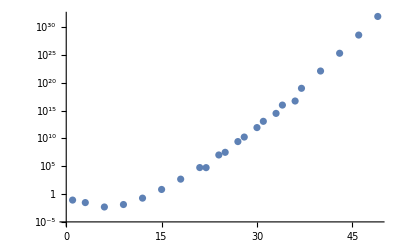

```mathematica
ListLogPlot[ϵpertCoeff]
```

```mathematica
ϵPertTrunc[h_, nmax_] := Normal[Series[ϵpert, {ℏ, 0, nmax}]]/.{ℏ->h}
```

```mathematica
ϵPertTrunc[1, 10]
```

0.003607398811381603266436078323654034748127935514920627395318435134741810614873508595696839056552251261432181036755660013168615125

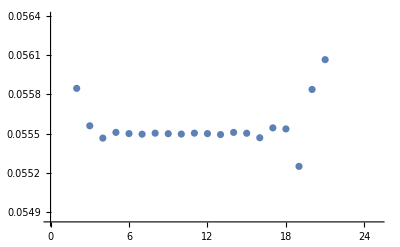

```mathematica
ListPlot[Table[ϵPertTrunc[0.4, nn], {nn,1,25}]]
```

## 4) Borel-Pade-Laplace transform

Setting ℏ=i directly during the numerical Laplace transform

```mathematica
BorelTransform[ϵpert_, ℏ_] := ϵpert/.{ℏ^nn_ -> ℏ^nn/nn!};
BorelPadeTransform[ϵpert_, ζ_,Padeorder_]:=PadeApproximant[BorelTransform[ϵpert, ℏ]/.{ℏ->ζζ}, {ζζ, 0, Padeorder}]/.{ζζ->ζ};
LaplaceTrafo[ϵpertBPT_] := NIntegrate[Exp[-t]ϵpertBPT/.ζ->I t,{t,0,∞},WorkingPrecision->prec,MaxRecursion->50];
```

```mathematica
ϵpertBPT = BorelPadeTransform[ϵpert, ζ, padeOrder];ϵBPLT = LaplaceTrafo[ϵpertBPT]; (*Borel-Pade-Laplace-transformed*)
```

NIntegrate::precw: The precision of the argument function ((ⅇ^-t (0.074577668328268684214151553815745797112072540303081246046426470558105033043900175876875905130559223562197995797333265663423770651382753720198+«34»+«119» ⅈ t^(«2»)))/(1+«36»+3.200256026201928735901579558131479217186830966506296311097600931512122083003632626606×10^-21 ⅈ t^25)) is less than WorkingPrecision (200.).

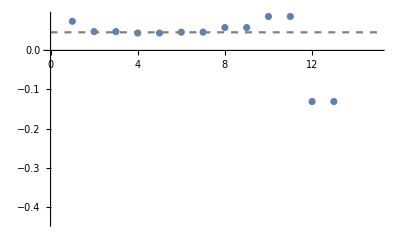

```mathematica
rePlot = ListPlot[Re@Table[ϵPertTrunc[I, nn], {nn,1,15}]];
reBPLT = Plot[Re@ϵBPLT, {nn,0,15}, PlotStyle->{Gray, Dashed}];
Show[rePlot, reBPLT]
```

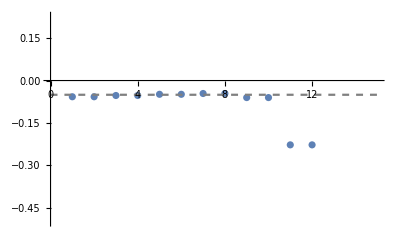

```mathematica
imPlot = ListPlot[Im@Table[ϵPertTrunc[I, nn], {nn,1,15}]];
imBPLT = Plot[Im@ϵBPLT, {nn,0,15}, PlotStyle->{Gray, Dashed}];
Show[imPlot, imBPLT]
```

```mathematica
ϵBPLT
```

0.04634612127858250187906654438348125165464698129585420581374466846876894920679994811498899355112796438552938385170502042341741019271744605802136805812712493932669202293466578388591005036754529502145724-0.050353153413361598362629801260973405722161088077941446396715634217570023656534312770507428213065182444886122702709979269727297955981980385596771696006388891368225873476278257209263264299763303328553686 ⅈ

## 5) Transform back to ω

```mathematica
ω[ϵBPLT_] := Sqrt[-(v[0] + 2 I ϵBPLT)];
PolesTable[ϵpertBPT_] := ζ/.Solve[NumeratorDenominator[ϵpertBPT][[2]]==0, ζ];
```

```mathematica
ω[ϵBPLT]//N
```

0.220881-0.209824 ⅈ

## Additional: Poles in the Borel Plane

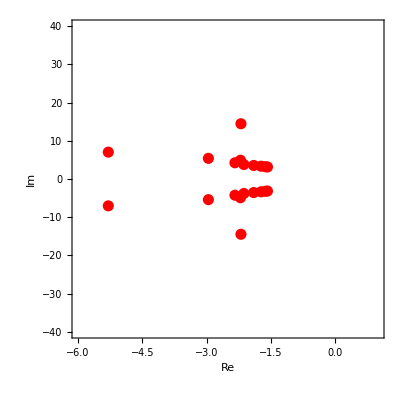

```mathematica
polesTable = PolesTable[ϵpertBPT];
ListPlot[{Re[#],Im[#]}&/@(Flatten@polesTable),AxesOrigin->{0,0},ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]],
PlotRange->{{-6, 1},{-40, 40}}]
```